```mathematica
data=ReadList["~/Software/BOS/build/tests/dist.dat",{Number,Number,Number}];
datap=Partition[data,11];
```

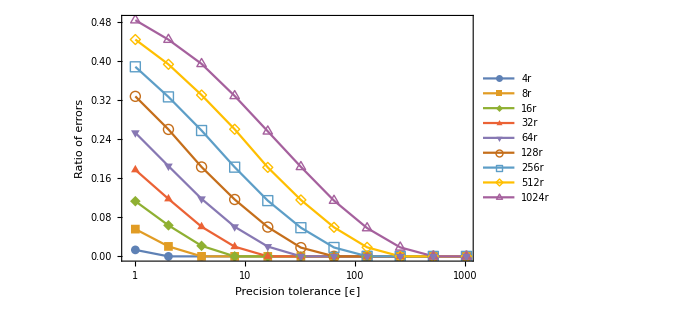

```mathematica
ListLogLinearPlot[Legended[{2^#[[2]],#[[3]]/100000}&/@#,ToString[#[[1,1]]]<>"r"]&/@datap[[All,All,{1,2,3}]],Frame->True,Joined->True,PlotMarkers->Automatic,PlotRange->All,FrameTicks->{Table[2^n,{n,0,9}],Automatic,None,None},FrameLabel->{"Precision tolerance [ϵ]","Ratio of errors"},ImageSize->500]
```